## 449 HW#1

#### 1) Show that the components of the momentum operator commute: [(p̂)_x,(p̂)_y]=0.

[(p̂)_x,(p̂)_y]ψ=-ⅈ ℏ [∂_x,∂_y]ψ=-ⅈ ℏ(∂_x ∂_y -∂_y ∂_x)ψ=0

#### 2) Let p be the eigenvectors of the momentum operator, with eigenvalues ℏ k, and r the eigenvectors of the position operator. Find the position representation rp of the momentum eigenstates.

-ⅈ ℏ∇ ⅇ^(ⅈ k·r)=ℏ k ⅇ^(ⅈ k·r)→rp =ⅇ^(ⅈ k·r)

#### 3) Show that in a region of space with V(r)=const, E=(ℏ^2 k^2)/(2 m)+V are the eigenvalues of the Schrodinger equation, and p are the eigenvectors.

H=(p̂)^2/(2m)+V; [p̂,H]=0→ E=(ℏ^2 k^2)/(2 m)+V

#### 4) Snell’s law for matter waves: suppose V(r)={V_0 | z<0 V_1 | z>0. A beam of particles with momentum ℏ k_i impinges upon the plane z=0, with ẑ·k_i=k_i cos(θ_i). At z=0, the beam is partially reflected and partially transmitted. Show that the reflected beam has ẑ·k_r=- k_icos(θ_i), and find the value of ẑ·k_t=k_t cos(θ_t) for the transmitted beam.

The boundary condition at z=0 must hold for all values of x & y.  Thus ⅇ^(ⅈ k_ix x+ⅈ k_iy y)=ⅇ^(ⅈ k_rx x+ⅈ k_ry y)=ⅇ^(ⅈ k_tx x+ⅈ k_ty y).  Thus k_rx=k_ix,k_ry=k_iy, k_rz=-k_iz, with the minus sign showing that the z-component of the momentum is reversed for the reflected wave.  Likewise k_tx=k_ix. Also we have ℏ^2 k_i^2+2m V_0=ℏ^2 k_t^2+2m V_1 Hence k_i sin(θ_i)=k_t sin(θ_t)→sin(θ_t)=sin(θ_i)k_i/(√(k_i^2+(2m)/ℏ^2(V_0-V_1)))

#### 5) Fresnel coefficients for matter waves: Use boundary conditions at z=0 to find the amplitudes of the reflected and transmitted beams.

psi continuous → ⅇ^(ⅈ k_i·r)+r ⅇ^(ⅈ k_r·r)|_(z=0)=t ⅇ^(ⅈ k_t·r)|_(z=0)→ 1+r=t
gradient continuous →∂_z ( ⅇ^(ⅈ k_i·r)+r ⅇ^(ⅈ k_r·r))|_(z=0)=∂_z t ⅇ^(ⅈ k_t·r)|_(z=0)→ ⅈ (k_iz+r k_r_z)=ⅈ k_tz t→ k_iz-r k_r_z=k_tz t

```mathematica
Solve[{Subscript[k, iz]-r Subscript[k, iz]==Subscript[k, tz] t ,1+r==t},{r,t}]
```

{{r→-(-k_iz+k_tz)/(k_iz+k_tz),t→(2 k_iz)/(k_iz+k_tz)}}

#### 6) Let V_0=0, V_1=(ℏ^2 Q^2)/(2m). Plot the transmitted probability as a function of k_i, for θ_i=45^o.

let u=k_i/Q

```mathematica
Subscript[θ, t]=ArcSin[Sin[π/4] u/(√(u^2-1))];
```

```mathematica
Ptrans=1-Abs[-(-Subscript[k, iz]+Subscript[k, tz])/(Subscript[k, iz]+Subscript[k, tz])]^2//.{Subscript[k, iz]->Q u Cos[π/4],Subscript[k, t]-> Q √(u^2-1^2),Subscript[k, tz]-> Subscript[k, t] Cos[ArcSin[Sin[π/4] u/(√(u^2-1))]]}//Simplify
```

1-Abs[(u-√(-2+u^2))/(u+√(-2+u^2))]^2

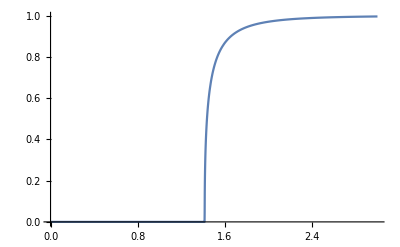

```mathematica
Plot[Ptrans//.{Subscript[k, iz]->Q u Cos[π/4],Subscript[k, t]->Q √(u^2-1^2),Subscript[k, tz]-> Subscript[k, t] Cos[ArcSin[Sin[π/4] u/(√(u^2-1))]]},{u,0,3},{PlotRange->All}]
```

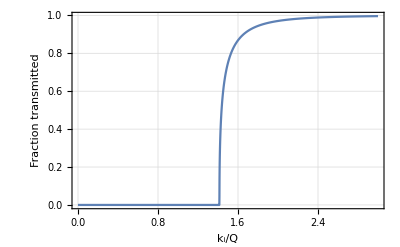

```mathematica
ThadPlot[%,{"k_i/Q","Fraction transmitted"}]
```

#### 7) Why is the beam totally reflected for Q<k<1.4 Q?

ℏ^2 k_i^2=ℏ^2 k_t^2+ℏ^2 Q^2
k_ix^2+k_iz^2=k_tx^2+k_tz^2+Q^2→k_iz^2=k^2 cos[θ_i]^2=k_tz^2+Q^2→k_tz^2=k^2 cos[θ_i]^2-Q^2

Therefore k_tz^2<0 for k<Q/cos[θ_i]=√2 Q  . The transmitted beam is exponentially damped (evanescent) for k<√2 Q.

#### 8) Suppose that in 2 dimensions the potential energy is V(x,y)=V_x(x)+V_y(y), so that H=H_x(x)+H_y(y). Calculate [H_x,H_y] and use your result to argue that the eigenstates must be of the form ψ(x,y)=ψ_x(x)ψ_y(y). Find the Schrödinger equations obeyed by ψ_x and ψ_y.

H_x=p_x^2/(2m)+V_x, H_y=p_y^2/(2m)+V_y, [H_x,H_y]=0 so the eigenstates are eigenstates of both H_x and H_y.  ψ_x ψ_y fits the bill. H_x ψ_x=E_x ψ_x,H_y ψ_y=E_y ψ_y, E=E_x+E_y.

#### 9) Find the energies and eigenstates for motion in the potential V(x,y)=Piecewise[{{1/2 κ x^2, 0<y<a}, {∞, Elsewhere}}]. Name your two quantum numbers n_x and n_y. Plot the lowest 10 energy levels for the case (m a^4 κ)/ℏ^2=π^4/4and be sure to note any degeneracies.

This is of the right form: V_x=1/2 κ x^2, V_y={0 | 0<y<a
∞ | Elsewhere.  Thus E =√(ℏ^2 κ/m)(n_x+1/2)+(ℏ^2 π^2)/(2m a^2)n_y^2=(ℏ^2 π^2)/(2m a^2)(n_y^2+√((4 a^4 m κ)/(π^4 ℏ^2))(n_x+1/2))=(ℏ^2 π^2)/(2m a^2)(n_y^2+n_x+1/2)

```mathematica
<<"http://tinyurl.com/pl27fdu"
```

```mathematica
{nxs,nys,energies}=(Table[{Subscript[n, x],Subscript[n, y],Subscript[n, y]^2+Subscript[n, x]+1/2},{Subscript[n, y],1,5},{Subscript[n, x],0,5}]~Flatten~1)ᵀ
```

{{0,1,2,3,4,5,0,1,2,3,4,5,0,1,2,3,4,5,0,1,2,3,4,5,0,1,2,3,4,5},{1,1,1,1,1,1,2,2,2,2,2,2,3,3,3,3,3,3,4,4,4,4,4,4,5,5,5,5,5,5},{3/2,5/2,7/2,9/2,11/2,13/2,9/2,11/2,13/2,15/2,17/2,19/2,19/2,21/2,23/2,25/2,27/2,29/2,33/2,35/2,37/2,39/2,41/2,43/2,51/2,53/2,55/2,57/2,59/2,61/2}}

```mathematica
in=Ordering[energies]⟦;;10⟧
```

{1,2,3,4,7,5,8,6,9,10}

here’s a list of the lowest energy levels, along with their n_x and n_y values.

```mathematica
{nxs⟦in⟧,nys⟦in⟧,energies⟦in⟧}ᵀ
```

{{0,1,3/2},{1,1,5/2},{2,1,7/2},{3,1,9/2},{0,2,9/2},{4,1,11/2},{1,2,11/2},{5,1,13/2},{2,2,13/2},{3,2,15/2}}

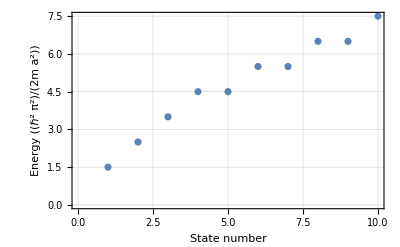

```mathematica
ThadPlot[ListPlot[energies⟦in⟧],{"State number","Energy ((ℏ^2 π^2)/(2m a^2))"}]
```

#### 10) Write the function f=sin^3 θ cos θ sin(3 ϕ) as a series of spherical harmonics.

```mathematica
Sum[Subscript[Y, l,m] Integrate[Sin[θ]^3 Cos[ θ] Sin[3 ϕ] SuperStar[SphericalHarmonicY[l,m,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2π}],{l,3,9},{m,{-3,3}}]
```

4/3 ⅈ √(π/35) Y_(4,-3)+4/3 ⅈ √(π/35) Y_(4,3)

#### 11) Calculate ∫ⅆΩ Y_(1,-1)(θ,ϕ)Y_(2,1)(θ,ϕ)Y_(3,0)(θ,ϕ) Y_(2,0)(θ,ϕ) by expanding each pair of Y’s as a series of spherical harmonics and using the orthogonality of the Y's.

```mathematica
Sum[Subscript[Y, l,m] Integrate[SphericalHarmonicY[1,-1,θ,ϕ]SphericalHarmonicY[2,1,θ,ϕ] SuperStar[SphericalHarmonicY[l,m,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2π}],{l,1,3},{m,0,0}]
```

-1/2 √(3/(5 π)) Y_(1,0)+(3 Y_(3,0))/(2 √(35 π))

```mathematica
Sum[Subscript[Y, l,m] Integrate[SphericalHarmonicY[3,0,θ,ϕ]SphericalHarmonicY[2,0,θ,ϕ] SuperStar[SphericalHarmonicY[l,m,θ,ϕ]] Sin[θ],{θ,0,π},{ϕ,0,2π}],{l,1,3},{m,0,0}]
```

3/2 √(3/(35 π)) Y_(1,0)+(2 Y_(3,0))/(3 √(5 π))

so ∫Y Y Y Y=∫(-1/2 √(3/(5 π)) Y_(1,0)+(3 Y_(3,0))/(2 √(35 π)))(3/2 √(3/(35 π)) Y_(1,0)+(2 Y_(3,0))/(3 √(5 π)))ⅆΩ=(-1/2 √(3/(5 π)) 3/2 √(3/(35 π))+3/(2 √(35 π))2/(3 √(5 π)))=-1/(4 √7 π)

#### 12) Find the lowest 8 energy levels (and their degeneracies) for the potential V= b r.

scaled variables (m a^3 b)/ℏ^2=1→ a=(ℏ^2/(m b))^(1/3),  (m a^2)/ℏ^2 E=ϵ =E (m/(ℏ^2 b^2))^(1/3),

```mathematica
dr=0.02;rs=Range[dr,10,dr];num=Length[rs];ones[n_]:=1+0Range[n];
psq=1/dr^2(2 DiagonalMatrix[ones[num]]-DiagonalMatrix[ones[num-1],1]-DiagonalMatrix[ones[num-1],-1]);
```

```mathematica
With[{l=0},eval=Sort[Eigenvalues[1/2 psq+DiagonalMatrix[(l(l+1))/(2  rs^2)+rs]]]⟦;;5⟧]
```

{1.85571,3.24447,4.38142,5.38623,6.30473}

```mathematica
With[{l=1},eval=Sort[Eigenvalues[1/2 psq+DiagonalMatrix[(l(l+1))/(2  rs^2)+rs]]]⟦;;5⟧]
```

{2.66779,3.87668,4.92678,5.87754,6.75807}

```mathematica
With[{l=2},eval=Sort[Eigenvalues[1/2 psq+DiagonalMatrix[(l(l+1))/(2  rs^2)+rs]]]⟦;;5⟧]
```

{3.37176,4.46822,5.45166,6.35702,7.20403}

```mathematica
With[{l=3},eval=Sort[Eigenvalues[1/2 psq+DiagonalMatrix[(l(l+1))/(2  rs^2)+rs]]]⟦;;5⟧]
```

{4.0089,5.02573,5.95629,6.82329,7.64088}

```mathematica
With[{l=4},eval=Sort[Eigenvalues[1/2 psq+DiagonalMatrix[(l(l+1))/(2  rs^2)+rs]]]⟦;;5⟧]
```

{4.59902,5.55526,6.44254,7.27669,8.06854}

```mathematica
{{n, l, deg, ϵ}, {0, 0, 1, 1.856}, {0, 1, 3, 2.668}, {1, 0, 1, 3.244}, {0, 2, 5, 3.372}, {1, 1, 3, 3.877}, {0, 3, 7, 4.009}, {2, 0, 1, 4.381}, {1, 2, 5, 4.468}, {2, 1, 3, 4.927}}
```

another approach: use PIAB basis.

```mathematica
dr=0.02;rs=Range[dr,10,dr];num=Length[rs];
```

```mathematica
upiab=Table[Sin[n π rs/10],{n,50}];upiab=Normalize/@upiab;
```

```mathematica
H[l_]=DiagonalMatrix[1/2 π^2/10^2 Range[50]^2]+upiab.DiagonalMatrix[rs+(l*(l+1))/(2 rs^2)].upiabᵀ;
```

```mathematica
es=Table[Eigenvalues[H[l]]⟦-5;;-1⟧,{l,0,3}]//Flatten
```

{6.30526,5.38661,4.38167,3.24461,1.85576,6.75914,5.87838,4.9274,3.87709,2.668,7.20444,6.35731,5.45184,4.4683,3.37178,7.64126,6.82354,5.95644,5.0258,4.00892}

```mathematica
nls=Table[{n,l},{l,0,3},{n,4,0,-1}]~Flatten~1
```

{{4,0},{3,0},{2,0},{1,0},{0,0},{4,1},{3,1},{2,1},{1,1},{0,1},{4,2},{3,2},{2,2},{1,2},{0,2},{4,3},{3,3},{2,3},{1,3},{0,3}}

```mathematica
in=Ordering[Flatten@es]
```

{5,10,4,15,9,20,3,14,8,19,2,13,7,18,1,12,6,17,11,16}

```mathematica
MatrixForm[Prepend[Table[{nls⟦i⟧,2nls⟦i,2⟧+1,es⟦i⟧}//Flatten,{i,in⟦;;9⟧}],{"n","l","deg","ϵ"}]]
```

(n | l | deg | ϵ
0 | 0 | 1 | 1.85576
0 | 1 | 3 | 2.668
1 | 0 | 1 | 3.24461
0 | 2 | 5 | 3.37178
1 | 1 | 3 | 3.87709
0 | 3 | 7 | 4.00892
2 | 0 | 1 | 4.38167
1 | 2 | 5 | 4.4683
2 | 1 | 3 | 4.9274)

yet another, more laborious, approach: Direct integration of the SE.  Boundary condition at small s is ψ=s^(l+1)
Integrate in from 10 to 1, then out from 0 to 1, compare logarithmic derivatives at s=1

```mathematica
SE[ϵ_,l_]:=-1/2 psi''[s]+(s+(l(l+1))/(2 s^2)) psi[s]==ϵ psi[s]
```

```mathematica
BCout[l_]={psi[.001]==(.001)^(l+1),psi'[.001]==(l+1)(.001)^l}
```

{psi[0.001]==0.001^(1+l),psi'[0.001]==0.001^l (1+l)}

```mathematica
BCin={psi[10]==1,psi'[10]==-1}
```

{psi[10]==1,psi'[10]==-1}

For l=1:

{-3.07843×10^-6}

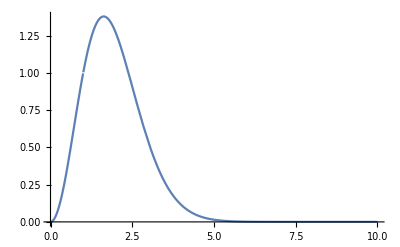

```mathematica
With[{ϵ=2.66783,l=1},
solin=NDSolve[{SE[ϵ,l],BCin},psi,{s,10,1}]⟦1⟧;
ψin[s_]:=psi[s]/.solin;
solout=NDSolve[{SE[ϵ,l],BCout[l]},psi,{s,.001,1}]⟦1⟧;
ψout[s_]:=psi[s]/.solout;
Print[{ψout'[1]/ψout[1]-ψin'[1]/ψin[1]}];
Plot[Piecewise[{{ψout[y]/ψout[1], y<1}, {ψin[y]/ψin[1], y>1}}],{y,.001,10},PlotRange->All]
]
```